```mathematica
Needs["FLUKAmatica`"]
```

To plot with error bars, not needed for importing data:

```mathematica
Needs["ErrorPlot`"]
```

Change relative error from % to usual ratio (for plotting):

```mathematica
ErrorToRel[data_]:=Map[{1,1,1,0.01}*#&,data]
```

## Energy distributions (USRTRACK & USRBDX)

### From doubly-differential USRBDX using energy integrated results

```mathematica
BDX2Integrated=ImportSingleBDX[Import[FileNameJoin[{NotebookDirectory[],"demo","demo_21_tab.lis"}],"Text"]];
```

```mathematica
TableForm[BDX2Integrated[[1]],TableHeadings->{None,{"Emin","Emax","Fluence","%Error"}}]
```

Emin | Emax | Fluence | %Error
0.1 | 0.136 | 0.009448 | 1.213
0.136 | 0.172 | 0.007167 | 4.109
0.172 | 0.208 | 0.005367 | 2.866
0.208 | 0.244 | 0.003888 | 4.68
0.244 | 0.28 | 0.003089 | 4.077
0.28 | 0.316 | 0.002765 | 1.162
0.316 | 0.352 | 0.002206 | 3.371
0.352 | 0.388 | 0.001843 | 4.866
0.388 | 0.424 | 0.001381 | 8.898
0.424 | 0.46 | 0.001241 | 7.291
0.46 | 0.496 | 0.001236 | 11.21
0.496 | 0.532 | 0.00106 | 9.003
0.532 | 0.568 | 0.000938 | 3.21
0.568 | 0.604 | 0.0007435 | 10.38
0.604 | 0.64 | 0.0007238 | 8.645
0.64 | 0.676 | 0.0007985 | 9.253
0.676 | 0.712 | 0.0007381 | 6.121
0.712 | 0.748 | 0.0007204 | 9.435
0.748 | 0.784 | 0.0008202 | 3.778
0.784 | 0.82 | 0.0009051 | 10.12
0.82 | 0.856 | 0.004138 | 2.038
0.856 | 0.892 | 0.02697 | 0.2438
0.892 | 0.928 | 0.00006399 | 12.42
0.928 | 0.964 | 0.00002764 | 14.25
0.964 | 1. | 3.93×10^-6 | 99.

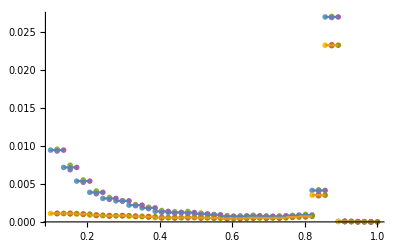

```mathematica
ErrorPlot[ErrorToRel/@BDX2Integrated,PlotErrorBars->{True,True},PlotRange->All,DataFormat->{"xMin","xMax","y","yRel"}]
```

### From singly-differential USRBDX

```mathematica
BDX1=ImportSingleBDX[Import[FileNameJoin[{NotebookDirectory[],"demo","demo_22_tab.lis"}],"Text"]];
```

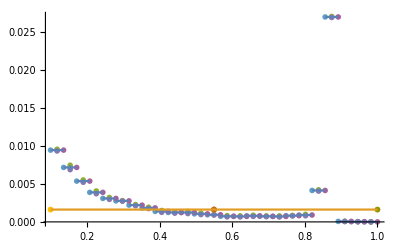

```mathematica
ErrorPlot[ErrorToRel/@BDX1,PlotErrorBars->{True,True},PlotRange->All,DataFormat->{"xMin","xMax","y","yRel"}]
```

The second dector is diferential only in angles. It is treated as double differential, hence a single bin is shown.

Check with the previous method:

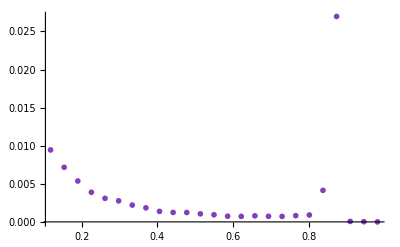

```mathematica
ErrorPlot[{BDX1[[1]],BDX2Integrated[[1]]},PlotErrorBars->False,PlotRange->All,PlotStyle->{Opacity[0.5,Red],Opacity[0.5,Blue]},DataFormat->{"xMin","xMax","y","yRel"}]
```

### USRTRACK

```mathematica
Track=ImportSingleBDX[Import[FileNameJoin[{NotebookDirectory[],"demo","demo_23_tab.lis"}],"Text"]];
```

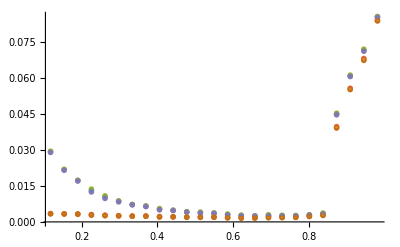

```mathematica
ErrorPlot[ErrorToRel/@Track,PlotErrorBars->{False,True},PlotRange->All,DataFormat->{"xMin","xMax","y","yRel"}]
```

Check fluence-energy fluence relationship

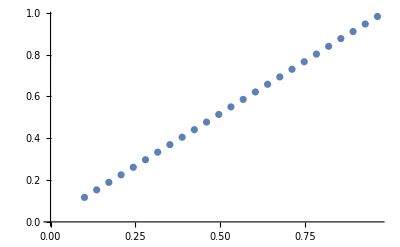

```mathematica
Transpose[{Track[[1,All,1]],Track[[2,All,3]]/Track[[1,All,3]]}]//ListPlot
```

## Doubly-differential USRBDX

TODO: Only partial support is added at the moment.

```mathematica
BDX2=ImportDoubleBDX[Import[FileNameJoin[{NotebookDirectory[],"demo","demo_21_tab.lis"}],"Text"]];
```

Each detector is in the following form

```mathematica
det=BDX2[[1]];
```

Angle mesh

```mathematica
det[[1]]
```

{{0.,0.502655},{0.502655,1.00531},{1.00531,1.50796},{1.50796,2.01062},{2.01062,2.51327},{2.51327,3.01593},{3.01593,3.51858},{3.51858,4.02124},{4.02124,4.52389},{4.52389,5.02655},{5.02655,5.5292},{5.5292,6.03186},{6.03186,6.53451},{6.53451,7.03717},{7.03717,7.53982},{7.53982,8.04248},{8.04248,8.54513},{8.54513,9.04779},{9.04779,9.55044},{9.55044,10.0531},{10.0531,10.5558},{10.5558,11.0584},{11.0584,11.5611},{11.5611,12.0637},{12.0637,12.5664}}

Energy mesh

```mathematica
det[[2]]
```

{{0.1,0.136},{0.136,0.172},{0.172,0.208},{0.208,0.244},{0.244,0.28},{0.28,0.316},{0.316,0.352},{0.352,0.388},{0.388,0.424},{0.424,0.46},{0.46,0.496},{0.496,0.532},{0.532,0.568},{0.568,0.604},{0.604,0.64},{0.64,0.676},{0.676,0.712},{0.712,0.748},{0.748,0.784},{0.784,0.82},{0.82,0.856},{0.856,0.892},{0.892,0.928},{0.928,0.964},{0.964,1.}}

Magnitude scored

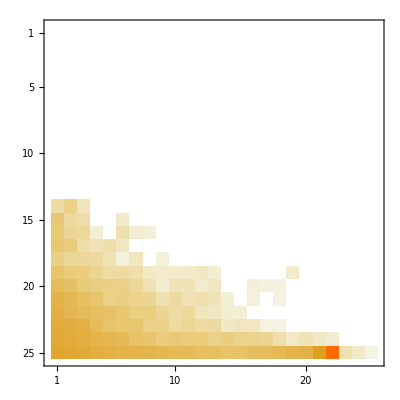

```mathematica
BDX2[[1]][[3]]//MatrixPlot
```

Errors

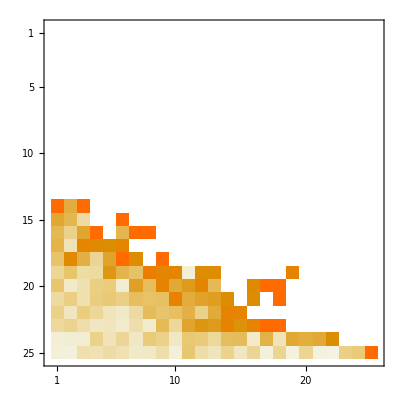

```mathematica
BDX2[[1]][[4]]//MatrixPlot
```